# The Structure of Orbigraphs

```mathematica
AppendTo[$Path,NotebookDirectory[]];
<<"Orbigraphs.m";
<<"MarkovOrbigraphs.m";
<<"OrbigraphCovers.m";
<<"UniversalCoverings.m";
```

## Orbifold Coverings

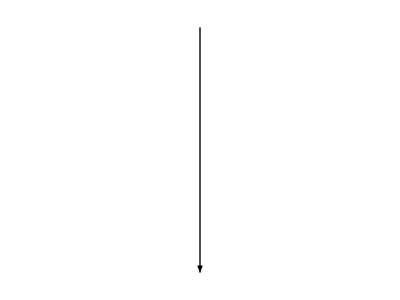
| -Graphics3D- | Manifold Cover | 
 | -Graphics- |  | 
 | -Graphics3D- | Orbigraph |

```mathematica
football = RevolutionPlot3D[{.5*(1-x^2),x},{x,-1,1},{θ,0,2π},Mesh->{5,10},PlotStyle->Blue,Axes->False,Boxed->False];

sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π},PlotStyle->Blue,Mesh->12, Axes->False,Boxed->False];
partSphere = RevolutionPlot3D[{Sqrt[1.04-t^2],t},{t,-1.04,1.05},{θ,-Pi/3+Pi/30,0},Mesh->{10,1},PlotStyle->Red, Axes->False,Boxed->False];

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];


Grid[
{
{
Spacer[5],
Show[sphere,partSphere],
Style["Manifold Cover", "Subsection"],
Spacer[5]
},

{
Spacer[8],
dwnArrw,
Spacer[2],
Spacer[5]
},
{
Spacer[3],
football,
Style["Orbigraph","Subsection"],
Spacer[5]
}
},
Alignment->Center,
ItemSize->{{Scaled[.2], Scaled[.3],Scaled[.2], Scaled[.2]}}
]
```

## Good and Bad Orbifolds

```mathematica
teardrop=Piecewise[{{1/Sqrt[3]*x,x≤Sqrt[3]},{Sqrt[4/3-(x-4/Sqrt[3])^2],Sqrt[3]<x≤2*Sqrt[3]}}];
cone=RevolutionPlot3D[{teardrop,-x},{x,0,1},{θ,0,2π},Mesh->{5,10},PlotRange->{{-2,2},{-2,2},{-4,0}},PlotStyle->Red];
bulb=RevolutionPlot3D[{teardrop,-x},{x,1,2Sqrt[3]},{θ,0,2π},Mesh->{10,10},PlotRange->{{-2,2},{-2,2},{-4,0}},Exclusions->None,PlotStyle->Blue];

football = RevolutionPlot3D[{.5*(1-x^2),x},{x,-1,1},{θ,0,2π},Mesh->{5,10},PlotStyle->Blue,Axes->False];

sphere = RevolutionPlot3D[{Sqrt[1-t^2],t},{t,-1,1},{θ,0,2π},PlotStyle->Blue, Axes->False];

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];

f[x_, y_] := Sqrt[(1 -y^2)*.3*(1 - 5*x^2)];
t = Plot3D[f[x,y], {x, -1,1},{y,-1,1}, AxesLabel->{x,y, z},Boxed->False,Axes->False, PlotStyle->Blue];
b =  Plot3D[-f[x,y], {x, -1,1},{y,-1,1}, AxesLabel->{x,y, z},Boxed->False,Axes->False, PlotStyle->Blue];
torus = RevolutionPlot3D[{3+Cos[t], Sin[t]}, {t, 0, 2Pi},Boxed->False, Axes->False,PlotStyle->Blue,BoundaryStyle->None];


planeBig = Plot3D[.9 ,{x,-1,1}, {y,-1,1}, PlotStyle->Green, Mesh-> {11,11}, Axes->False, Boxed->False];
planeSmall = RegionPlot3D[-1/3≤ x && x ≤ 1/3 && -1/3 ≤ y && y≤ 1/3 && z<.91 && z > .5,{x, -1, 1}, {y, -1, 1}, {z, 0, 2} ,PlotStyle->Blue,Axes->False, Boxed->False,Mesh->{3,3},PlotPoints->25];

Grid[
{

{
Spacer[5],
Style["Good Orbifold", "Subsection"],
Style["Bad Orbifold", "Subsection"],
Spacer[5]
},
{Spacer[5],
Spacer[5],
Spacer[5],
Spacer[5]
},
{
Spacer[5],
Show[planeBig, planeSmall],
Show[bulb, cone, SphericalRegion->True,Axes->False,Boxed->False],
Spacer[5]
},

{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},

{
Spacer[5],
torus,
Magnify[Text[Style["𝓍", Red, 24]], 4],
Spacer[5]
},
{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},
{
Spacer[5],
Show[t, b, PlotRange->{{-1,1},{-1,1}, {-1,1}},ImageSize->{230, 230}],
Show[bulb, cone, SphericalRegion->True,Axes->False,Boxed->False],
Spacer[5]
}
},
Alignment->{{Left, Right}},
ItemSize->{{Scaled[.2], Scaled[.3], Scaled[.3], Scaled[.2]}}
]
```

| Good Orbifold | Bad Orbifold | 
 |  |  | 
 | -Graphics3D- | -Graphics3D- | 
 | -Graphics- | -Graphics- | 
 | -Graphics3D- | 𝓍 | 
 | -Graphics- | -Graphics- | 
 | -Graphics3D- | -Graphics3D- |

## Quotients and Covering Graphs

```mathematica
grassman1=PermutationGroup[{
Cycles[{{1,2},{3,4}}],
Cycles[{{1,3},{2,4}}],
Cycles[{{1,4},{2,3}}]
}];
cover=CompleteGraph[6,VertexSize->0.3, VertexLabels->Table[i -> i, {i, 1, 6}]];


highlightCover = HighlightGraph[cover, CompletePartition[cover, GroupOrbits[grassman1]]];
highlightCover =SetProperty[highlightCover, 
{
VertexStyle->{
1->Red,
2->Red,
3->Red,
4->Red,
5->Yellow,
6->Purple
},
VertexShapeFunction->{
1->"Square",
2->"Square",
3->"Square",
4->"Square",
5->"Triangle",
6->"Star"}
}
];

orbigraph1=OrbigraphFromGroup[cover, grassman1];
orbigraph1 = SetProperty[orbigraph1, 
{
VertexSize->.2,
VertexShapeFunction-> {1->"Square", 2-> "Triangle", 3->"Star"}, 
VertexStyle->{1-> Red, 2->Yellow, 3->Purple}
}
];

Column[{
PaneSelector[
{
1 -> Style["What is a covering graph?","Subsection"],
2-> Style["What is an equitable partition?", "Subsection"], 
3-> Style["How do we quotient?","Subsection"]
},
Dynamic[time],
TransitionEffect->"Fade",
 Alignment->Center],
Slider[Dynamic[time], {1, 3, 1}],
PaneSelector[
{
1 -> SetProperty[cover,ImageSize->{300,300}],
2-> SetProperty[highlightCover,ImageSize->{300,300}] ,
3-> Grid[
{
{
SetProperty[highlightCover, ImageSize->{300,300}], 
Spacer[100],SetProperty[orbigraph1, ImageSize->{300,300}]
}
}, 
ItemSize->Full]
},
Dynamic[time],
ImageSize->Full, 
TransitionEffect->"Fade",
 Alignment->Center]
},Center]
```

## From Orbifolds to Graphs: Good and Bad Orbigraphs

```mathematica
dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.5},{0,-.5}}]}];

badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .1,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,3},{1,2}}],
{
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square"
}
}
];

goodCover = CreateFiniteCoveringGraph[Normal@WeightedAdjacencyMatrix@goodOrbi];



goodUCover = SetProperty[CreateUniversalCovering[goodOrbi,4], VertexSize->.3];
badUCover = SetProperty[CreateUniversalCovering[badOrbi,4], VertexSize->.3];

showcover = False
Grid[
{
{
Spacer[5],
Style["Good Orbigraph", "Subsection"],
Style["Bad Orbigraph", "Subsection"],
Spacer[5]
},
{
Spacer[5],
goodUCover,
badUCover,
Spacer[5]
},
{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},
{
Spacer[5],
goodCover,
Magnify[Text[Style["𝓍", Red, 24]], 4],
Spacer[5]
},
{
Spacer[5],
dwnArrw,
dwnArrw,
Spacer[5]
},
{
Spacer[5],
goodOrbi,
badOrbi,
Spacer[5]
}
},
Alignment->{{Left, Right}},
ItemSize->{{Scaled[.2], Scaled[.3], Scaled[.3], Scaled[.2]}}
]
```

False

| Good Orbigraph | Bad Orbigraph | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | 𝓍 | 
 | -Graphics- | -Graphics- | 
 | -Graphics- | -Graphics- |

## Universal Covering Tree

```mathematica
sizes = SetProperty[CreateUniversalCovering[orbigraph1, #], VertexSize-> .2] &/@ Range[3];

GraphPlotRange[graph_Graph] := With[{embedding = GraphEmbedding@graph},
{{Min[First /@ embedding]-1, Max[First/@embedding]+1},{Min[Last/@embedding]-1, Max[Last/@embedding]+1}}]

(*
biggest = Last@sizes;

sizes =SetProperty[#, 
{
VertexCoordinates-> Take[GraphEmbedding@Last@sizes, VertexCount@#],
PlotRange-> GraphPlotRange[biggest]
}
]&/@
sizes;
*)
Row[{
SetProperty[orbigraph1,ImageSize->{300,300}],
Spacer[50],
ListAnimate[sizes, DefaultDuration->3]
}]
```

-Graphics-

## Characterization of Good and Bad Orbigraphs

Good: only “balanced” cycles

Bad: at least one “unbalanced” cycle

```mathematica
badOrbi = SetProperty[
AdjacencyOrbigraph[{{0,2,1},{1,0,2},{2,1,0}}],
{
VertexSize -> .1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->Large,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

goodOrbi = SetProperty[
AdjacencyOrbigraph[{{0,1,1},{1,0,2},{1,2,0}}],
{
VertexSize->.1,
EdgeStyle->Directive[Thick, Black],
EdgeLabelStyle->Large,
VertexStyle->
{
1 -> Red,
2-> Yellow,
3->Purple
},
VertexShapeFunction->
{
1-> "Triangle",
2->"Square",
3->"Star"
}
}
];

dwnArrw = Graphics[{Arrowheads[.1],Arrow[{{0,.3},{0,-.3}}]}];

edgesToHighlight = {
{{}, Green},
{1->2, Green},
{2->3, Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red}
};

textFrames = {
{"", "Subsection"},
{"2", "Subsection"},
{"2×2", "Subsection"},
{"2×2×2", "Subsection"},
{"2×2×2≠1", "Subsection"},
{"2×2×2≠1×1", "Subsection"},
{"2×2×2≠1×1×1", "Subsection"}
};

edgesToHighlight2 = {
{{}, Green},
{1->2,Green},
{2->3,Green},
{3->1,Green},
{1->3,Red},
{3->2,Red},
{2->1,Red}
};

textFrames2= {
{"", "Subsection"},
{"1", "Subsection"},
{"1×2", "Subsection"},
{"1×2×1", "Subsection"},
{"1×2×1=1", "Subsection"},
{"1×2×1=1×2", "Subsection"},
{"1×2×1=1×2×1", "Subsection"}
};

kolmogorov=
Manipulate[
Column[{
SetProperty[
HighlightGraph[badOrbi,
Style[
First@edgesToHighlight⟦#⟧,
Directive[Last@edgesToHighlight⟦#⟧, Thick]
]&/@Range[d]
],
ImageSize->{300,300}],
Spacer[20],
Row[{
Spacer[20],
Style[
First@textFrames⟦d⟧,
Last@textFrames⟦d⟧
]
}]
}
],
 {d, 1, 7,1}];

kolmogorov2 = 
Manipulate[
Column[{
SetProperty[
HighlightGraph[goodOrbi,
Style[
First@edgesToHighlight2⟦#⟧,
Directive[Last@edgesToHighlight2⟦#⟧, Thick]
]&/@Range[d]
],
ImageSize->{300,300}],
Spacer[20],
Row[{
Spacer[20],
Style[
First@textFrames2⟦d⟧,
Last@textFrames2⟦d⟧
]
}]
}
],

 {d, 1, 7,1}];

Grid[
{

{
Spacer[300],
Style["Good Orbigraph", "Subsection"],
Spacer[5],
Style["Bad Orbigraph", "Subsection"],
Spacer[5]
},
{
Spacer[5],
kolmogorov2,
Spacer[.1],
kolmogorov,
Spacer[5]
}
},
Alignment->{Center}
]
```

| Good Orbigraph |  | Bad Orbigraph | 
 |  |  |  |

## Example: Good Orbigraph

Let’s pick a random good orbigraph and construct a covering

```mathematica
GenerateRandomReversibleOrbigraph[n_, k_] := Module[{randOrbi = GenerateRandomOrbigraph[n, k], tries=0},
While[tries ≤ 400 && Not[ConnectedOrbigraphQ[randOrbi]] || Not[OrbigraphReversibleQ[randOrbi]],
randOrbi = GenerateRandomOrbigraph[n, k];
tries++;
];
Return[randOrbi];
]

randOrbi = Style["Nothing", "Subsubsection"];
coveringGraph = Style["Nothing", "Subsubsection"];

Row[{
Spacer[300],
Column[{
Button["Generate Random Orbigraph", 
Dynamic[
coveringGraph = Style["Nothing", "Subsubsection"];
randOrbi = GenerateRandomReversibleOrbigraph[3,3];

randOrbi = SetProperty[
AdjacencyOrbigraph@randOrbi,
{
VertexSize->.3,
ImageSize->{450,300},
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
]
]
],

Button["Generate Finite Covering",
Dynamic[coveringGraph = SetProperty[
CreateFiniteCoveringGraph[WeightedAdjacencyMatrix@randOrbi],
{ImageSize->{300,300}, GraphLayout->"SpringEmbedding"}
];
]
],
Dynamic[coveringGraph],
dwnArrw,
Dynamic[randOrbi]
},
Alignment->Center
]
}
]
```

Generate Random Orbigraph
Generate Finite Covering

-Graphics-

## How did we discover and prove this connection?

Comes from Markov chain property “reversibility”

Reversible Markov chains satisfy the balance equation: π_i P_(i, j)= π_j P_(j,i)

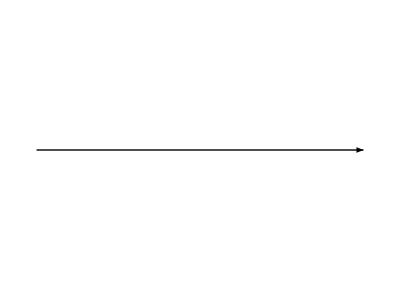
-Graphics--Graphics-

```mathematica
rightArrw = Graphics[{Arrowheads[.1],Arrow[{{-1.5,0},{1.5,0}}]}];
shortRightArrw = Graphics[{Arrowheads[.1],Arrow[{{0,0},{.3,0}}]}];

ro ={{0,2,1},{3,0,0},{2,0,1}};
P = ro/3;

markovChain = MarkovProcessFromOrbigraph@ro;

ro = SetProperty[
AdjacencyOrbigraph@ro,
{
ImageSize->{300,300},
VertexLabels->{1->1,2->2,3->3},
VertexSize->.1,
VertexStyle->
{
1-> Red, 
2-> Yellow,
3->Purple
},
 VertexShapeFunction->
{
1-> "Triangle", 
2-> "Square",
3->"Star"
}
}
];

totalCounts = 0;

GenerateRandomWalk[chain_DiscreteMarkovProcess, len_Integer] :=Module[{counts ,walk= {}, cur=1,next,i,  G = Graph@chain, T=Normal@MarkovProcessProperties[chain, "TransitionMatrix"]},
cur = RandomChoice[VertexList@G];
counts = {ConstantArray[0, VertexCount@G]};

 For[i = 0, i < len, i++, 
next = RandomChoice[Cases[T⟦cur⟧, x_/;x ≠ 0]-> Flatten[Position[T⟦cur⟧, x_/;x ≠ 0],1]];
walk = Append[walk, next];
counts = Append[counts, Last@counts];
counts⟦Length@counts,next⟧++; 
cur = next;
];

Return[{walk, counts}];
]


w = GenerateRandomWalk[markovChain, 5000];
normalizedOrbigraph = SetProperty[ro, {EdgeWeight-> N[PropertyValue[ro, EdgeWeight]/3], ImageSize->{300, 200}}];

Row[{
Spacer[50],
ro,
Spacer[20],
rightArrw,
Spacer[20],
Manipulate[
Grid[
{
{
HighlightGraph[normalizedOrbigraph, {Style[(First@w)⟦t⟧, Lighter@Pink]}],
Spacer[20],
Style[StringJoin@{"π = [",Riffle[ToString@NumberForm[#,{2,2}]&/@N[(Last@w)⟦t⟧/t],", ", 2], "]"}, "Subsubsection"]
},
{
Grid[
{
{
Style["π_1P_(1, 2) = π_2P_(2, 1)", "Subsubsection"],Style["π_1P_(1, 3) = π_3P_(3, 1)", "Subsubsection"]
},
{
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .31, P⟦1,2⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[t ≥ 4500, .31, P⟦2,1⟧ * N[(Last@w)⟦t⟧/t]⟦2⟧],{2,2}]
},
"Subsubsection"],
Style[StringJoin@{
ToString@NumberForm[If[t ≥ 4500, .16, P⟦1,3⟧ * N[(Last@w)⟦t⟧/t]⟦1⟧],{2,2}],
" = ", 
ToString@NumberForm[If[ t ≥ 4500, .16, P⟦3,1⟧ * N[(Last@w)⟦t⟧/t]⟦3⟧],{2,2}]
},
"Subsubsection"]
}
},
Frame->All,
Spacings->{3,1}
]
}

}
]
,
{t, 1, Length@First@w, 1}
]}
,
Alignment->Center
]
```

## Conclusion

Orbigraphs are graph theoretic analogues of Riemannian Orbifolds

We can distinguish good and bad orbigraphs

We can bound the number of singular points using the spectrum

## Acknowledgements

Dr. Liz Stanhope

Miller Foundation

Lewis & Clark College